# Multi-way tag systems in coordinatized Rulial space

Dean Song Gladish

Carleton Class of 2020
Mentor James Boyd @ WSS 2022

These are lovely systems; suppose we want infinite feedback and at the same time want the graph to continue on generating indefinitely.

Abstract.
The multi-way tag system, a topic in computational complexity based on Emil Post’s tag system, is that provided the positive integer v and µ symbols taken to be 0, 1, ..., µ-1, the association with each of the µ symbols is a finite sequence as follows. 

0 -> a_(0, 1)a_(0, 2) . . . a_(0, v_0)
0 -> a_(1, 1)a_(1, 2) . . . a_(1, v_0)
. . . . . . . . . .
µ - 1 -> a_(µ - 1)a_(µ - 1, 2) . . . a_(µ-1, v_(µ-1))

For such a simple basis as 0->00, 1->1101, v=3, it’s an effective procedure for determining of an arbitrary initial sequence.^4 My project focuses on the Post decision for a special type of normal system, faithfully per Post’s discovery that his tag operation is applicable in binary space. 

To advance our understanding of computational irreducibility, my project studies the behavior of tag systems with different rules & initial conditions, evaluated as single-way rules and multi-way tag systems. My project focuses on comparing single-way and multi-way behavior, exploring explosive, degenerate, and cyclic behavior, and visualizing novel instances of the Ruliology. Generating analogues of Turing Machine Groups with multi-way tag systems, the work provides a new coordinatized method for studying the Ruliad and Rulial space.

## The Post Tag System

The basis that Post mentions, is the goal of this project that is, such a simple basis as 0->00, 1->1101. Furthermore, single-element and two-element spatial tag systems can be generated via the multi-way graph, starting from different initial conditions. The analyzability of this project starts systematically via the law of excluded middle starting with the single characters 1 and 0. 

Given all binary numbers 0, 1, 00, 01, 10, 11, 000, 001, etc. remove the first digit for the initial conditions. And for the rules, the same kind of thing so regardless of whether the update is put at the right or left hand side of the string, the multi-way system generated via string-rewriting is called a stag system because it’s about a spatial tag system; a system that can do its update from any point in space. 

Therefore, visualize a multi-way tag system based on Post’s conjecture, which increments depending on the value of the tag system rules, depending on the dimensionality of the rule cycle sequence which generates paths; when the tag system rules increase dimensionality the string demonstrates explosive behavior, and when the tag system rules decrease dimensionality the string demonstrates degenerate behavior. For dimensionality we create the generational plot, provided that the Post tag system describes extreme, either-or cases for rule length. 

Provided that the rules are re-writing strings to greater lengths, most four-rule tag systems appear to be exploding. But first, let us look at the Post tag system with initial condition 101.

## The Post Tag System, With Initial Condition 1.

As we know the Post Tag System with initial condition 0 is absolutely trivial. However, initial condition 1 brings us to a general exhibition of the Post Tag System.

```mathematica
Dean=Labeled[
Graph[
ResourceFunction["MultiwaySystem"][
{"0"->"00","1"->"1101"},
{"1"},
3,
"StatesGraph",
ImageSize->1000,
Frame->{{True,False},
{True,False}}],
Epilog->{
ResourceFunction["WolframPhysicsProjectStyleData"]["BranchialGraph",
"EdgeStyle"],
AbsoluteThickness[.5],
Table[Line[{{-8,i},{10,i}}],
{i,1/2,6+1/2}]
}],
StringTemplate["{0}->`a` 
{1}->`b` 
`e`"][<|"a"->{0,0},
"b"->{1,1,0,1},
"e":>{1}|>]]
```

-Graphics-{0}->{0, 0} 
{1}->{1, 1, 0, 1} 
{1}

Suppose that Post’s tag system, unless we want the left side of our string to be comprised exclusively of 0s, is mostly accessible via the input size of 1. The first and last 1s are merged because we are mapping rule 1->1101 recursively.

## The Post Tag System, With Initial Condition 101.

```mathematica
Dean=Labeled[
Graph[
ResourceFunction["MultiwaySystem"][
{"0"->"00","1"->"1101"},
{"101"},
3,
"StatesGraph",
ImageSize->1000,
Frame->{{True,False},
{True,False}}],
Epilog->{
ResourceFunction["WolframPhysicsProjectStyleData"][
"BranchialGraph",
"EdgeStyle"
],
AbsoluteThickness[.5],
Table[Line[{{-8,i},{10,i}}],
{i,1/2,6+1/2}]
}],
StringTemplate["{0}->`a` 
{1}->`b` 
`e`"][<|"a"->{0,0},
"b"->{1,1,0,1},
"e":>{1,0,1}|>]]
```

-Graphics-{0}->{0, 0} 
{1}->{1, 1, 0, 1} 
{1, 0, 1}

The Post tag system is describing string re-writing, and for that there are two rules and three levels in the graph. This tag system is describing the string re-writing. The initial condition of 101 via the MultiwaySystem API determines the direction of time within the graph.

## Section 1. Functions & Dependencies.

Emil Post began determining whether the iterative process of tag was terminating, periodic, or divergent, which is with regard to computational complexity the major project of his tenure of a Procter fellowship in mathematics at Princeton during the academic year 1920-21.^5

To properly and clearly describe the evolution of the Post Tag System, the Wolfram Language code is presented in a clear narrative format, to explain how Post’s tag system is studied and how the tag system is degenerate, periodic, or exploding. As a result, the sections demarcate each major step function & point of clarification/pivot.

### Sub-section 1. Make Shifted Tag System with Four-Set of Rules.

The implementation with NestGraph, that is NestList turned into edges between corresponding elements, and the generation of graphs with layered di-graph embedding, portrays the evolution of new tag systems in the Wolfram Language Code; ResourceFunction[“NestGraphTagged”] serves the function of differently tagging edges corresponding to different outputs.^3

The NestGraphTagged function allows us to plot Tag System 2.

```mathematica
Multicolumn[
Table[
ResourceFunction["NestGraphTagged"][
ReplaceList[{
{left___,0,0,s___}:>{left,s,1,0,0},
{left___,1,0,s___}:>{left,s,1},
{left___,0,1,s___}:>{left,s,1,1,0},
{left___,1,1,s___}:>{left,s,0,1}}],
{{1,1}},
i,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality",
ImageSize->Automatic,
Epilog->{ResourceFunction["WolframPhysicsProjectStyleData"][
"BranchialGraph",
"EdgeStyle"
],
AbsoluteThickness[.1],
Table[Line[{{-8,i},{10,i}}],{i,1/2,6+1/2}],
Table[Line[{{i,-8},{i,10}}],{i,1/2,6+1/2}]
}
],
{i,1,8}]]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

The graph of the string re-writing, for which Multicolumn allows the Table to be set as a value, denotes the function. Differentiating between branches at each step, we can show functions for Tag System 2 because the cyclic flexibility of the single-element is shown in each row, that is showing the maintenance of, for time steps from previous columns, the three-cycle type steps.

Define MultiwayTagSystem as its own function.

```mathematica
MultiwayTagSystem[rule_,init_,t_]:=ResourceFunction["NestGraphTagged"][
rule,
init,
t,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality",
ImageSize->Full
]
```

```mathematica
MultiwayTagSystem[ReplaceList[{
{left___,0,0,s___}:>{left,s,1,0,0},
{left___,1,0,s___}:>{left,s,1},
{left___,0,1,s___}:>{left,s,1,1,0},
{left___,1,1,s___}:>{left,s,0,1}}],
{{1,1}},
8
]
```

-Graphics-

In this format, it’s very beautiful. But what is the point of showing this? To make the multi-way system understandable.

Plot the MultiwayTagSystem vertex list against its complement.

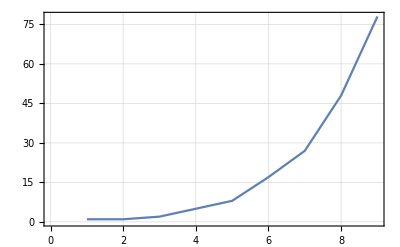

```mathematica
ListLinePlot[
With[{rules=ReplaceList[{
{left___,0,0,s___}:>{left,s,1,0,0},
{left___,1,0,s___}:>{left,s,1},
{left___,0,1,s___}:>{left,s,1,1,0},
{left___,1,1,s___}:>{left,s,0,1}}]},
Table[
Length[
Complement[
VertexList[MultiwayTagSystem[rules,
{{1,1}},
t
]],
VertexList[MultiwayTagSystem[rules,
{{1,1}},
t-1
]]
]],
{t,2,10}
]],
PlotTheme->"Detailed",
ImageSize->Automatic
]
```

ListLinePlot continuity between discrete points on the length of inductively unique vertices.

MultiwayTagSystem function on Tag System 2.

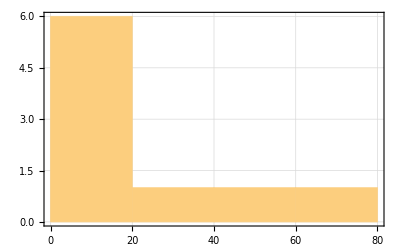

```mathematica
Histogram[
With[{rules=ReplaceList[{
{left___,0,0,s___}:>{left,s,1,0,0},
{left___,1,0,s___}:>{left,s,1},
{left___,0,1,s___}:>{left,s,1,1,0},
{left___,1,1,s___}:>{left,s,0,1}}]},
Table[
Length[
Complement[
VertexList[MultiwayTagSystem[rules,
{{1,1}},
t
]],
VertexList[MultiwayTagSystem[rules,
{{1,1}},
t-1
]]
]],
{t,2,10}]],
5,
PlotTheme->"Detailed"
]
```

Visualize Tag System Multi-Way. The RandomMultiwayTagSystem function.

```mathematica
RandomMultiwayTagSystem[g_]:=Table[ArrayPlot[Reverse@Transpose[PadRight[With[
{
vertices=VertexList[g],randomInit=Table[RandomInteger[{0,1},3],8]
},
Table[
FindShortestPath[g,First[VertexList[g]],vertices[[i]]],
{i,1,Length[vertices]}
]][[i]],
{Automatic,Automatic},
.25]],
Frame->True,
ColorRules->{0->Hue[.95,.4,1.4],1->Hue[.1,.1,.1]},
Mesh->True],
{i,1,Length[VertexList[g]]}]
```

The RandomMultiwayTagSystem function generates all distributed stag systems for Tag System 3.

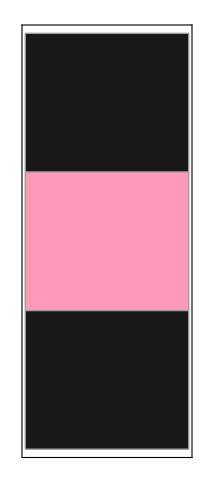
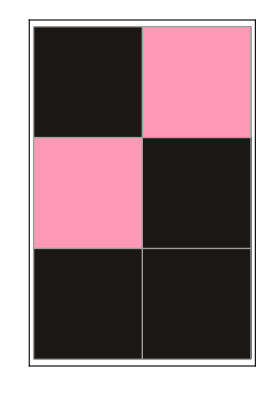
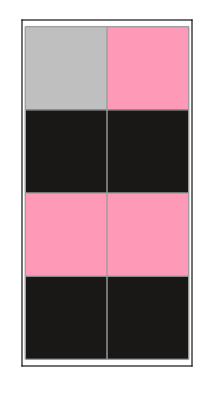
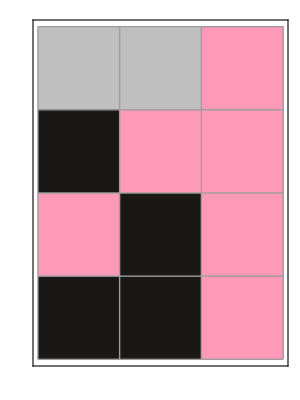
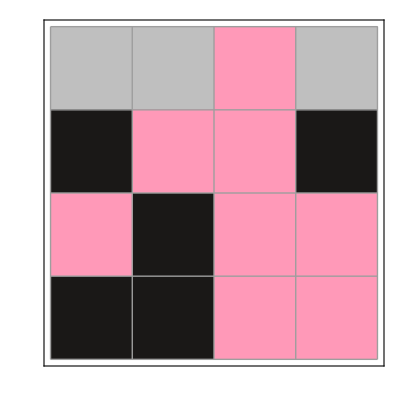
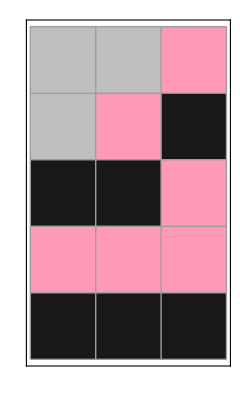
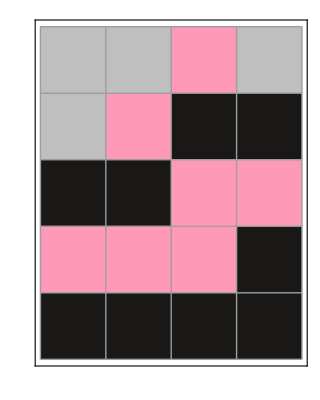
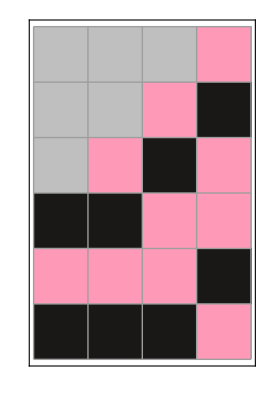

```mathematica
RandomMultiwayTagSystem[ResourceFunction["NestGraphTagged"][ReplaceList[{
{left___,0,0,s___}:>{left,s,1},
{left___,1,0,s___}:>{left,s,0,1,0},
{left___,0,1,s___}:>{left,s,1,0},
{left___,1,1,s___}:>{left,s,0,0,0}
}],
{{1,0,1}},
3,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"]]
```

Suppose we want to vary the fourth rule of Tag System 3.

```mathematica
generateAllDistributedStagSystem[
l1_,l2_,l3_,l4_,
i1R_,i2R_,i3R_,i4R_,
init_,
timeSteps_
]:=Multicolumn[Table[
Labeled[ResourceFunction["NestGraphTagged"][ReplaceList[{
{left___,0,0,s___}:>Flatten[{left,s,Tuples[{0,1},l1][[i1]]}],
{left___,1,0,s___}:>Flatten[{left,s,Tuples[{0,1},l2][[i2]]}],
{left___,0,1,s___}:>Flatten[{left,s,Tuples[{0,1},l3][[i3]]}],
{left___,1,1,s___}:>Flatten[{left,s,Tuples[{0,1},l4][[i4]]}]
}],
{init},
t,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"],
StringTemplate["{0,0,s___}->`a`
{1,0,s___}->`b`
{0,1,s___}->`c`
{1,1,s___}->`d`
`e`"]
[<|
"a"->Tuples[{0,1},l1][[i1]],
"b"->Tuples[{0,1},l2][[i2]],
"c":>Tuples[{0,1},l3][[i3]],
"d":>Tuples[{0,1},l4][[i4]],
"e":>init
|>]
],
{t,1,timeSteps},
{i1, i1R[[1]],i1R[[2]]},
{i2,i2R[[1]],i2R[[2]]},
{i3,i3R[[1]],i3R[[2]]},
{i4,i4R[[1]],i4R[[2]]}]]
```

```mathematica
generateAllDistributedStagSystem[
1,3,2,3,
{2,2},{3,3},{3,3},{1,8},
{1,0,1},
5
]
```

{{{{-Graphics-{0,0,s___}->{1}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{0, 0, 0}
{1, 0, 1},-Graphics-{0,0,s___}->{1}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{0, 0, 1}
{1, 0, 1},-Graphics-{0,0,s___}->{1}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{0, 1, 0}
{1, 0, 1},-Graphics-{0,0,s___}->{1}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{0, 1, 1}
{1, 0, 1},-Graphics-{0,0,s___}->{1}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{1, 0, 0}
{1, 0, 1},-Graphics-{0,0,s___}->{1}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{1, 0, 1}
{1, 0, 1},-Graphics-{0,0,s___}->{1}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{1, 1, 0}
{1, 0, 1},-Graphics-{0,0,s___}->{1}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{1, 1, 1}
{1, 0, 1}}}}} | {{{{-Graphics-{0,0,s___}->{1}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{0, 0, 0}
{1, 0, 1},-Graphics-{0,0,s___}->{1}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{0, 0, 1}
{1, 0, 1},-Graphics-{0,0,s___}->{1}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{0, 1, 0}
{1, 0, 1},-Graphics-{0,0,s___}->{1}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{0, 1, 1}
{1, 0, 1},-Graphics-{0,0,s___}->{1}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{1, 0, 0}
{1, 0, 1},-Graphics-{0,0,s___}->{1}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{1, 0, 1}
{1, 0, 1},-Graphics-{0,0,s___}->{1}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{1, 1, 0}
{1, 0, 1},-Graphics-{0,0,s___}->{1}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{1, 1, 1}
{1, 0, 1}}}}} | {{{{-Graphics-{0,0,s___}->{1}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{0, 0, 0}
{1, 0, 1},-Graphics-{0,0,s___}->{1}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{0, 0, 1}
{1, 0, 1},-Graphics-{0,0,s___}->{1}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{0, 1, 0}
{1, 0, 1},-Graphics-{0,0,s___}->{1}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{0, 1, 1}
{1, 0, 1},-Graphics-{0,0,s___}->{1}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{1, 0, 0}
{1, 0, 1},-Graphics-{0,0,s___}->{1}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{1, 0, 1}
{1, 0, 1},-Graphics-{0,0,s___}->{1}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{1, 1, 0}
{1, 0, 1},-Graphics-{0,0,s___}->{1}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{1, 1, 1}
{1, 0, 1}}}}}
{{{{-Graphics-{0,0,s___}->{1}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{0, 0, 0}
{1, 0, 1},-Graphics-{0,0,s___}->{1}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{0, 0, 1}
{1, 0, 1},-Graphics-{0,0,s___}->{1}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{0, 1, 0}
{1, 0, 1},-Graphics-{0,0,s___}->{1}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{0, 1, 1}
{1, 0, 1},-Graphics-{0,0,s___}->{1}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{1, 0, 0}
{1, 0, 1},-Graphics-{0,0,s___}->{1}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{1, 0, 1}
{1, 0, 1},-Graphics-{0,0,s___}->{1}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{1, 1, 0}
{1, 0, 1},-Graphics-{0,0,s___}->{1}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{1, 1, 1}
{1, 0, 1}}}}} | {{{{-Graphics-{0,0,s___}->{1}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{0, 0, 0}
{1, 0, 1},-Graphics-{0,0,s___}->{1}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{0, 0, 1}
{1, 0, 1},-Graphics-{0,0,s___}->{1}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{0, 1, 0}
{1, 0, 1},-Graphics-{0,0,s___}->{1}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{0, 1, 1}
{1, 0, 1},-Graphics-{0,0,s___}->{1}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{1, 0, 0}
{1, 0, 1},-Graphics-{0,0,s___}->{1}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{1, 0, 1}
{1, 0, 1},-Graphics-{0,0,s___}->{1}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{1, 1, 0}
{1, 0, 1},-Graphics-{0,0,s___}->{1}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{1, 1, 1}
{1, 0, 1}}}}} |

Aside from varying the initial condition, we can also vary the fourth rule.

Five Time Steps for Tag System 3.

```mathematica
generatePathCanyon[
rule1_,
rule2_,
rule3_,
rule4_,
init_,
timeSteps_
]:=Multicolumn[Table[Labeled[ResourceFunction["NestGraphTagged"][ReplaceList[{
{left___,0,0,s___}:>Flatten[{left,s,rule1}],
{left___,1,0,s___}:>Flatten[{left,s,rule2}],
{left___,0,1,s___}:>Flatten[{left,s,rule3}],
{left___,1,1,s___}:>Flatten[{left,s,rule4}]
}],
{init},
t,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"],
StringTemplate["{0,0,s___}->`a`
{1,0,s___}->`b`
{0,1,s___}->`c`
{1,1,s___}->`d`
`e`"]
[<|
"a"->rule1,
"b"->rule2,
"c":>rule3,
"d":>rule4,
"e":>init
|>]
],
{t,1,timeSteps}]]
```

```mathematica
generatePathCanyon[
{1},
{0,1,0},
{1,0},
{0,0,0},
{1,0,1},
5
]
```

-Graphics-{0,0,s___}->{1}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{0, 0, 0}
{1, 0, 1} | -Graphics-{0,0,s___}->{1}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{0, 0, 0}
{1, 0, 1} | -Graphics-{0,0,s___}->{1}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{0, 0, 0}
{1, 0, 1}
-Graphics-{0,0,s___}->{1}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{0, 0, 0}
{1, 0, 1} | -Graphics-{0,0,s___}->{1}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{0, 0, 0}
{1, 0, 1} |

ListStepPlots, for Post’s Tag System.

```mathematica
ruleAllListStepPlotsInitialConditions[lengthInitialConditionR_,lastTimeStep_]:=
Table[ListStepPlot[Legended[FlattenAt[
 Table[
Style[Text[
With[
{
graph = NestGraph[
ReplaceList[{
{0,left___,left___,s___}:>{s,0,0},
{1,left___,left___,s___}:>{s,1,1,0,1}
}],
{Tuples[{0,1},i][[j]]},
timeStep,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"
]
},
Table[
Length /@FindShortestPath[graph,First[VertexList[graph]],VertexList[graph][[v]]],
{v,1,Length[VertexList[graph]]}
]
]]][[1]][[1]],
{timeStep,1,lastTimeStep}
]
,
{#}&/@Range[lastTimeStep]],Tuples[{0,1},i][[j]]]],
{i,lengthInitialConditionR[[1]],lengthInitialConditionR[[2]]},
{j,1,2^i}]
```

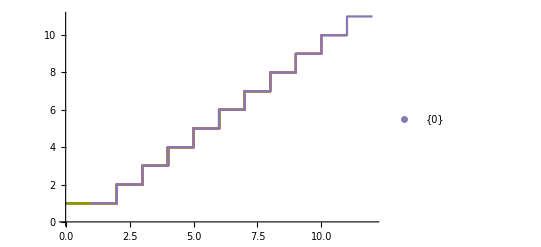
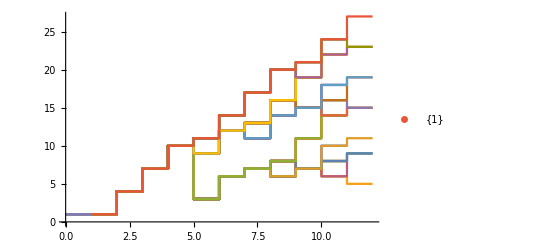
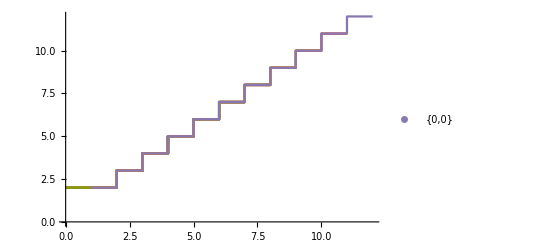
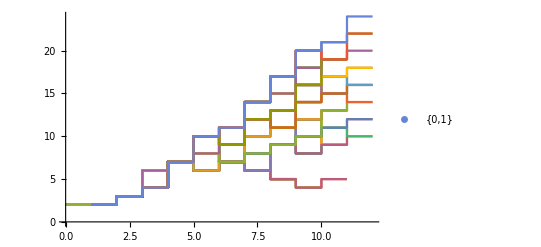
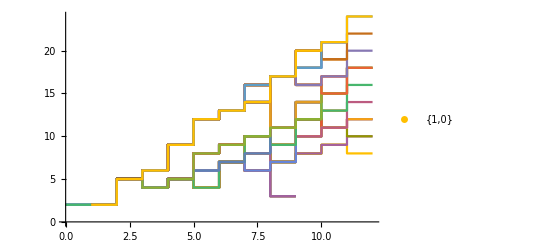
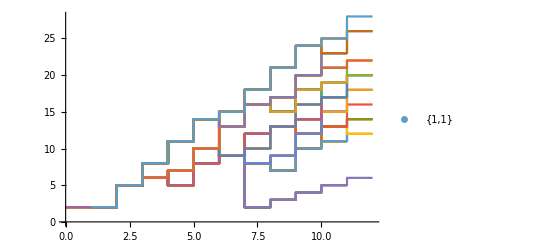
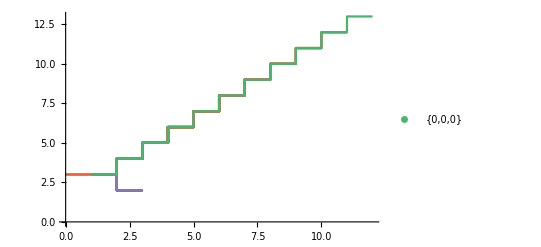
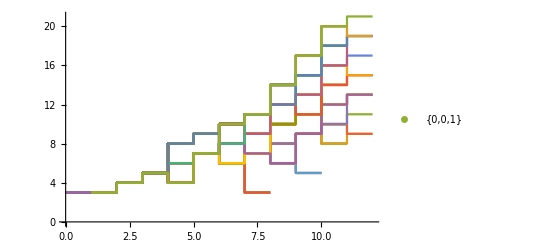

```mathematica
ruleAllListStepPlotsInitialConditions[{1,3}, 10]
```

Binary function, finds the binary path of all path canyons like Tag System 2.

```mathematica
AllPathCanyonsBinary[g_]:=Style[Text[Table[
Column[Row/@PadRight[
With[
{
vertices=VertexList[g],
randomInit=Tuples[{0,1},3]
},
Table[
FindShortestPath[g,First[VertexList[g]],vertices[[i]]],
{i,1,Length[vertices]}
]
][[j]],
{Automatic,Automatic},
.25
],Center]//. 0.25->"",
{j,2,Length[VertexList[g]]}
]//.{x_}:>x],FontFamily->"Roboto"]
```

```mathematica
Multicolumn[Table[
AllPathCanyonsBinary[
NestGraph[
ReplaceList[{
{left___,0,0,s___}:>Flatten[{left,s,1,0,0}],
{left___,1,0,s___}:>Flatten[{left,s,1}],
{left___,0,1,s___}:>Flatten[{left,s,1,1,0}],
{left___,1,1,s___}:>Flatten[{left,s,Tuples[{0,1},2][[i]]}]
}],
{{1,1}},
5,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"
]],
{i,1,4}
]]
```

{11
00,11
00
100,11
00
100
01,11
00
100
1100,11
00
100
01
110,11
00
100
1100
101,11
00
100
1100
0000,11
00
100
1100
11100,11
00
100
1100
101
1110,11
00
100
01
110
000,11
00
100
1100
0000
00100,11
00
100
1100
11100
1101,11
00
100
1100
11100
10000,11
00
100
1100
11100
111100} | {11
10,11
10
1}
{11
01,11
01
110,11
01
110
001,11
01
110
001
0110,11
01
110
001
1100,11
01
110
001
0110
011,11
01
110
001
0110
0001,11
01
110
001
0110
10110,11
01
110
001
1100
101,11
01
110
001
1100
11100} | {}

AllPathCanyons “generational” plots of binary tag systems.

```mathematica
AllPathCanyons[g_]:=Table[
ArrayPlot[
Reverse@Transpose[
PadRight[
With[
{
vertices=VertexList[g],
randomInit=Tuples[{0,1},3]
},
Table[
FindShortestPath[g,First[VertexList[g]],vertices[[i]]],
{i,1,Length[vertices]}
]
][[i]],
{Automatic,Automatic},
.25
]
],
Frame->True,
ColorRules->{0->Hue[.95,.4,1.4],
1->Hue[.1,.1,.1]},
Mesh->True
],
{i,1,Length[VertexList[g]]}
]
```

Tag System 1.

```mathematica
AllPathCanyons[
NestGraph[
ReplaceList[{
{left___,0,0,s___}:>{left,s,1,1,0},
{left___,1,0,s___}:>{left,s,0,1},
{left___,0,1,s___}:>{left,s,0,1},
{left___,1,1,s___}:>{left,s,0,1}}],
{{0,1,0}},
5,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"
]
]
```

AllPathCanyons[-Graphics-]

Tag System 4.

```mathematica
g := With[{
g=NestGraph[ReplaceList[{
{left___,0,0,s___}:>Flatten[{left,s,Tuples[{0,1},3][[5]]}],
{left___,1,0,s___}:>Flatten[{left,s,Tuples[{0,1},2][[3]]}],
{left___,0,1,s___}:>Flatten[{left,s,Tuples[{0,1},3][[1]]}],
{left___,1,1,s___}:>Flatten[{left,s,Tuples[{0,1},2][[1]]}]}],
{Tuples[{0,1},3][[1]]},
3,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality",
ImageSize->Large]},
Labeled[
HighlightGraph[
Graph[
g,
VertexLabels->Thread[VertexList[g]->(Length[#]&/@VertexList[g])]
],Style[PathGraph[FindShortestPath[g,First[VertexList[g]],VertexList[g][[Length[VertexList[g]]]]],DirectedEdges->True],Red]
],
StringTemplate["{0,0,s___}->`a`
{1,0,s___}->`b`
{0,1,s___}->`c`
{1,1,s___}->`d`
`e`"]
[<|
"a"->Tuples[{0,1},3][[5]],
"b"->Tuples[{0,1},2][[3]],
"c":>Tuples[{0,1},3][[1]],
"d":>Tuples[{0,1},2][[1]],
"e":>Tuples[{0,1},3][[1]]
|>]]]
g
```

-Graphics-{0,0,s___}->{1, 0, 0}
{1,0,s___}->{1, 0}
{0,1,s___}->{0, 0, 0}
{1,1,s___}->{0, 0}
{0, 0, 0}

### Sub-section GraphDistanceMatrix.

The Temperature Plot of an initial condition for all Graph Distance Matrices.

```mathematica
generateAllTemperaturePlots[
l1_,l2_,l3_,l4_,
i1R_,i2R_,i3R_,i4R_,
init_,
timeSteps_,
branchialGraph_:True,
matrixForm_:True
]:=With[{
graph=NestGraph[ReplaceList[
{
{left___,0,0,s___}:>Flatten[{left,s,Tuples[{0,1},l1][[i1]]}],
{left___,1,0,s___}:>Flatten[{left,s,Tuples[{0,1},l2][[i2]]}],
{left___,0,1,s___}:>Flatten[{left,s,Tuples[{0,1},l3][[i3]]}],
{left___,1,1,s___}:>Flatten[{left,s,Tuples[{0,1},l4][[i4]]}]
}
],
{init},
t,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"]
},
Table[
{
Labeled[
ArrayPlot[GraphDistanceMatrix[{{"[◼]", "BranchialGraph"}}[graph]]/.∞->0,ColorFunction->"TemperatureMap", PlotLegends->Automatic],
StringTemplate["{0,0,s___}->`a`
{1,0,s___}->`b`
{0,1,s___}->`c`
{1,1,s___}->`d`
`e`"]
[<|
"a"->Tuples[{0,1},l1][[i1]],
"b"->Tuples[{0,1},l2][[i2]],
"c":>Tuples[{0,1},l3][[i3]],
"d":>Tuples[{0,1},l4][[i4]],
"e":>init
|>]],
If[branchialGraph,{{"[◼]", "BranchialGraph"}}[graph],Null],
If[matrixForm,Style[MatrixForm[GraphDistanceMatrix[{{"[◼]", "BranchialGraph"}}[graph]]],FontSize->8],Null]
},
{t,1,timeSteps},
{i1, i1R[[1]],i1R[[2]]},
{i2,i2R[[1]],i2R[[2]]},
{i3,i3R[[1]],i3R[[2]]},
{i4,i4R[[1]],i4R[[2]]}
] 
]
```

```mathematica
generateAllTemperaturePlots[
3,3,3,3,
{6,8},{4,4},{8,8},{4,4},
{1,1,0},
5,
True,
True
]
```

NestGraph::intpm: Positive machine-sized integer expected at position 3 in NestGraph[ReplaceList[{{left$___,0,0,s$___}:>Flatten[{left$,s$,Tuples[«2»]⟦i1⟧}],{left$___,1,0,s$___}:>Flatten[{left$,s$,Tuples[«2»]⟦i2⟧}],{left$___,0,1,s$___}:>Flatten[{left$,s$,Tuples[«2»]⟦i3⟧}],{left$___,1,1,s$___}:>Flatten[{left$,s$,Tuples[«2»]⟦i4⟧}]}],{{1,1,0}},t].

{{{{{{-Graphics-{0,0,s___}->{1, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{1, 1, 1}
{1,1,s___}->{0, 1, 1}
{1, 1, 0},-Graphics-,(0 | 1
1 | 0)}}}},{{{{-Graphics-{0,0,s___}->{1, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{1, 1, 1}
{1,1,s___}->{0, 1, 1}
{1, 1, 0},-Graphics-,(0 | 1
1 | 0)}}}},{{{{-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{1, 1, 1}
{1,1,s___}->{0, 1, 1}
{1, 1, 0},-Graphics-,(0 | 1
1 | 0)}}}}},{{{{{-Graphics-{0,0,s___}->{1, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{1, 1, 1}
{1,1,s___}->{0, 1, 1}
{1, 1, 0},-Graphics-,(0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | 0 | 1 | 1 | ∞ | ∞ | ∞
∞ | ∞ | 1 | 0 | 1 | ∞ | ∞ | ∞
∞ | ∞ | 1 | 1 | 0 | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1
∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1
∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0)}}}},{{{{-Graphics-{0,0,s___}->{1, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{1, 1, 1}
{1,1,s___}->{0, 1, 1}
{1, 1, 0},-Graphics-,(0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | 0 | 1 | 1 | ∞ | ∞ | ∞
∞ | ∞ | 1 | 0 | 1 | ∞ | ∞ | ∞
∞ | ∞ | 1 | 1 | 0 | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1
∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1
∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0)}}}},{{{{-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{1, 1, 1}
{1,1,s___}->{0, 1, 1}
{1, 1, 0},-Graphics-,(0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞
1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | 0 | 1 | 1 | 2 | 2
∞ | ∞ | 1 | 0 | 1 | 2 | 2
∞ | ∞ | 1 | 1 | 0 | 1 | 1
∞ | ∞ | 2 | 2 | 1 | 0 | 1
∞ | ∞ | 2 | 2 | 1 | 1 | 0)}}}}},{{{{{-Graphics-{0,0,s___}->{1, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{1, 1, 1}
{1,1,s___}->{0, 1, 1}
{1, 1, 0},-Graphics-,(0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | 0 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | 1 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | 1 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 2
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | 2 | 2 | 1 | 2 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | 2 | 2 | 1 | 2 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 0 | 1 | 2 | 1 | 2
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 1 | 0 | 2 | 1 | 1
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 1 | 2 | 2 | 0 | 2 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 1 | 1 | 2 | 0 | 1
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 3 | 3 | 2 | 1 | 3 | 1 | 0)}}}},{{{{-Graphics-{0,0,s___}->{1, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{1, 1, 1}
{1,1,s___}->{0, 1, 1}
{1, 1, 0},-Graphics-,(0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | 0 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | 1 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | 1 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | 1 | 1 | 1 | 1
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | 2 | 2 | 1 | 2
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | 2 | 2 | 1 | 2
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 0 | 1 | 2 | 1
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 1 | 0 | 2 | 1
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 1 | 2 | 2 | 0 | 2
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 1 | 1 | 2 | 0)}}}},{{{{-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{1, 1, 1}
{1,1,s___}->{0, 1, 1}
{1, 1, 0},-Graphics-,(0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | 0 | 1 | 1 | 2 | 2 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | 1 | 0 | 1 | 2 | 2 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | 1 | 1 | 0 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | 2 | 2 | 1 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | 2 | 2 | 1 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | 1 | 1 | 1
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | 2 | 2 | 1
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | 2 | 2 | 1
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 0 | 1 | 1
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 1 | 0 | 1
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 1 | 1 | 1 | 0)}}}}},{{{{{-Graphics-{0,0,s___}->{1, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{1, 1, 1}
{1,1,s___}->{0, 1, 1}
{1, 1, 0},-Graphics-,(0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | 0 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | 1 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | 1 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | 2 | 2 | 1 | 2 | 3 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | 2 | 2 | 1 | 2 | 3 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 0 | 1 | 2 | 1 | 2 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 1 | 0 | 2 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 1 | 2 | 2 | 0 | 2 | 3 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 1 | 1 | 2 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 3 | 3 | 2 | 1 | 3 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | 1 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 4
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | 1 | 2 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 3 | 3 | 3 | 4
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 1 | 0 | 2 | 2 | 2 | 2 | 1 | 2 | 1 | 1 | 1 | 2 | 3 | 3 | 3 | 4
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 0 | 1 | 2 | 1 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 4
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 1 | 0 | 2 | 1 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 4
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 2 | 2 | 0 | 2 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 2
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 1 | 1 | 2 | 0 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 4
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 1 | 1 | 2 | 2 | 1 | 2 | 0 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 0 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 1 | 1 | 2 | 2 | 1 | 2 | 2 | 1 | 0 | 1 | 1 | 2 | 2 | 2 | 2 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 1 | 1 | 0 | 2 | 2 | 2 | 2 | 2 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 2 | 1 | 1 | 3 | 3 | 2 | 3 | 2 | 2 | 1 | 2 | 0 | 3 | 3 | 3 | 3 | 4
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 2 | 2 | 2 | 3 | 3 | 1 | 3 | 1 | 2 | 2 | 2 | 3 | 0 | 2 | 2 | 2 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 3 | 3 | 3 | 3 | 3 | 1 | 3 | 2 | 2 | 2 | 2 | 3 | 2 | 0 | 1 | 1 | 2
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 3 | 3 | 3 | 3 | 3 | 1 | 3 | 2 | 2 | 2 | 2 | 3 | 2 | 1 | 0 | 1 | 1
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 3 | 3 | 3 | 3 | 3 | 1 | 3 | 2 | 2 | 2 | 2 | 3 | 2 | 1 | 1 | 0 | 1
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 3 | 4 | 4 | 4 | 4 | 4 | 2 | 4 | 3 | 3 | 3 | 3 | 4 | 3 | 2 | 1 | 1 | 0)}}}},{{{{-Graphics-{0,0,s___}->{1, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{1, 1, 1}
{1,1,s___}->{0, 1, 1}
{1, 1, 0},-Graphics-,(0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | 0 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | 1 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | 1 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | 1 | 1 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | 2 | 2 | 1 | 2 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | 2 | 2 | 1 | 2 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 0 | 1 | 2 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 1 | 0 | 2 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 1 | 2 | 2 | 0 | 2 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 1 | 1 | 2 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | 1 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 1 | 3 | 3 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | 1 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 1 | 3 | 3 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 1 | 0 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 1 | 2 | 3 | 3 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 0 | 1 | 2 | 1 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 1 | 0 | 2 | 1 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 2 | 2 | 0 | 2 | 2 | 1 | 1 | 1 | 3 | 1 | 1 | 1
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 1 | 1 | 2 | 0 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 0 | 2 | 2 | 2 | 2 | 3 | 3 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 0 | 1 | 1 | 3 | 2 | 2 | 2
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 1 | 0 | 1 | 3 | 2 | 2 | 2
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 1 | 1 | 0 | 3 | 2 | 2 | 2
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 1 | 1 | 2 | 3 | 3 | 3 | 3 | 2 | 3 | 3 | 3 | 0 | 4 | 4 | 4
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 3 | 3 | 3 | 3 | 3 | 1 | 3 | 3 | 2 | 2 | 2 | 4 | 0 | 1 | 1
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 3 | 3 | 3 | 3 | 3 | 1 | 3 | 3 | 2 | 2 | 2 | 4 | 1 | 0 | 1
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 3 | 3 | 3 | 3 | 3 | 1 | 3 | 3 | 2 | 2 | 2 | 4 | 1 | 1 | 0)}}}},{{{{-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{1, 1, 1}
{1,1,s___}->{0, 1, 1}
{1, 1, 0},-Graphics-,(0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | 0 | 1 | 1 | 2 | 2 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | 1 | 0 | 1 | 2 | 2 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | 1 | 1 | 0 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | 2 | 2 | 1 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | 2 | 2 | 1 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | 1 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | 2 | 2 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | 2 | 2 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 0 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 1 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 1 | 1 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 2
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | 1 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 3 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | 1 | 2 | 2 | 2 | 1 | 2 | 2 | 1 | 2 | 2
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 1 | 0 | 2 | 2 | 2 | 1 | 2 | 2 | 1 | 2 | 2
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 0 | 1 | 2 | 1 | 2 | 2 | 2 | 3 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 1 | 0 | 2 | 1 | 2 | 2 | 2 | 3 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 2 | 2 | 0 | 2 | 1 | 1 | 1 | 1 | 1
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 0 | 2 | 2 | 2 | 3 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 0 | 1 | 1 | 2 | 2
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 1 | 0 | 1 | 2 | 2
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 1 | 1 | 2 | 2 | 1 | 2 | 1 | 1 | 0 | 1 | 1
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 3 | 2 | 2 | 3 | 3 | 1 | 3 | 2 | 2 | 1 | 0 | 1
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 3 | 2 | 2 | 3 | 3 | 1 | 3 | 2 | 2 | 1 | 1 | 0)}}}}},{{{{{-Graphics-{0,0,s___}->{1, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{1, 1, 1}
{1,1,s___}->{0, 1, 1}
{1, 1, 0},-Graphics-,(0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | 0 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | 1 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | 1 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | 2 | 2 | 1 | 2 | 3 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | 2 | 2 | 1 | 2 | 3 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 0 | 1 | 2 | 1 | 2 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 1 | 0 | 2 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 1 | 2 | 2 | 0 | 2 | 3 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 1 | 1 | 2 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 3 | 3 | 2 | 1 | 3 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 3 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | 1 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 4 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | 1 | 2 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 3 | 3 | 3 | 4 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 1 | 0 | 2 | 2 | 2 | 2 | 1 | 2 | 1 | 1 | 1 | 2 | 3 | 3 | 3 | 4 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 0 | 1 | 2 | 1 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 4 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 1 | 0 | 2 | 1 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 4 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 2 | 2 | 0 | 2 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 2 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 1 | 1 | 2 | 0 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 4 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 1 | 1 | 2 | 2 | 1 | 2 | 0 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 3 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 0 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 3 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 1 | 1 | 2 | 2 | 1 | 2 | 2 | 1 | 0 | 1 | 1 | 2 | 2 | 2 | 2 | 3 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 1 | 1 | 0 | 2 | 2 | 2 | 2 | 2 | 3 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 2 | 1 | 1 | 3 | 3 | 2 | 3 | 2 | 2 | 1 | 2 | 0 | 3 | 3 | 3 | 3 | 4 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 2 | 2 | 2 | 3 | 3 | 1 | 3 | 1 | 2 | 2 | 2 | 3 | 0 | 2 | 2 | 2 | 3 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 3 | 3 | 3 | 3 | 3 | 1 | 3 | 2 | 2 | 2 | 2 | 3 | 2 | 0 | 1 | 1 | 2 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 3 | 3 | 3 | 3 | 3 | 1 | 3 | 2 | 2 | 2 | 2 | 3 | 2 | 1 | 0 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 3 | 3 | 3 | 3 | 3 | 1 | 3 | 2 | 2 | 2 | 2 | 3 | 2 | 1 | 1 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 3 | 4 | 4 | 4 | 4 | 4 | 2 | 4 | 3 | 3 | 3 | 3 | 4 | 3 | 2 | 1 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 2 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | 1 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 3 | 4 | 3 | 3 | 4 | 4 | 3 | 3 | 4
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | 1 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 3 | 4 | 3 | 3 | 4 | 4 | 3 | 3 | 4
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 1 | 0 | 2 | 1 | 2 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 3 | 4 | 3 | 3 | 4 | 4 | 3 | 3 | 4
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 0 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 2 | 2 | 2 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 1 | 1 | 1 | 0 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 3 | 3 | 3 | 4
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 1 | 2 | 0 | 1 | 1 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 3 | 3 | 3 | 4
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 1 | 1 | 1 | 2 | 1 | 0 | 1 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 3 | 3 | 3 | 4
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 1 | 1 | 2 | 1 | 1 | 0 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 3 | 3 | 3 | 4
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 0 | 1 | 2 | 1 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 3 | 4 | 3 | 3 | 4 | 4 | 3 | 3 | 4
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 0 | 2 | 1 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 3 | 4 | 3 | 3 | 4 | 4 | 3 | 3 | 4
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 0 | 2 | 1 | 1 | 1 | 1 | 3 | 3 | 3 | 2 | 1 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 2 | 1 | 1 | 2 | 2 | 1 | 1 | 2
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 2 | 0 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 3 | 4 | 3 | 3 | 4 | 4 | 3 | 3 | 4
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 1 | 2 | 1 | 1 | 1 | 2 | 2 | 1 | 2 | 0 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 2 | 3 | 2 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 0 | 1 | 1 | 3 | 3 | 3 | 3 | 2 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 2 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 1 | 0 | 1 | 3 | 3 | 3 | 3 | 2 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 2 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 1 | 1 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 1 | 1 | 0 | 2 | 2 | 2 | 3 | 2 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 2 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 2 | 1 | 1 | 2 | 2 | 2 | 1 | 2 | 3 | 3 | 3 | 3 | 2 | 3 | 3 | 2 | 0 | 1 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 5 | 4 | 4 | 4 | 5
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 2 | 1 | 1 | 2 | 2 | 2 | 1 | 2 | 3 | 3 | 3 | 3 | 2 | 3 | 3 | 2 | 1 | 0 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 5 | 4 | 4 | 4 | 5
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 2 | 2 | 2 | 1 | 1 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 2 | 3 | 3 | 2 | 3 | 3 | 0 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 3 | 3 | 3 | 4
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 3 | 3 | 3 | 1 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 2 | 0 | 1 | 1 | 2 | 2 | 1 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 3 | 3 | 3 | 1 | 2 | 2 | 2 | 2 | 3 | 3 | 1 | 3 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 1 | 0 | 1 | 2 | 1 | 1 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 3 | 3 | 3 | 1 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 2 | 1 | 1 | 0 | 2 | 2 | 1 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 3 | 3 | 3 | 1 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 0 | 1 | 1 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 2 | 2 | 2 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 3 | 3 | 3 | 1 | 2 | 2 | 2 | 2 | 3 | 3 | 1 | 3 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 2 | 1 | 2 | 1 | 0 | 1 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 2
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 3 | 3 | 3 | 1 | 2 | 2 | 2 | 2 | 3 | 3 | 1 | 3 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 1 | 1 | 1 | 1 | 1 | 0 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 1 | 1 | 2 | 2 | 2 | 2 | 2
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 3 | 3 | 3 | 2 | 3 | 2 | 2 | 2 | 3 | 3 | 1 | 3 | 1 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 2 | 3 | 3 | 2 | 2 | 0 | 1 | 1 | 2 | 3 | 2 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 3 | 3 | 3 | 2 | 3 | 2 | 2 | 2 | 3 | 3 | 1 | 3 | 1 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 2 | 3 | 3 | 2 | 2 | 1 | 0 | 1 | 2 | 3 | 2 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 3 | 3 | 3 | 2 | 3 | 2 | 2 | 2 | 3 | 3 | 1 | 3 | 1 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 2 | 3 | 3 | 2 | 2 | 1 | 1 | 0 | 2 | 3 | 2 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 3 | 3 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 1 | 3 | 2 | 2 | 2 | 2 | 4 | 4 | 3 | 2 | 1 | 2 | 2 | 1 | 1 | 2 | 2 | 2 | 0 | 2 | 1 | 2 | 1 | 1 | 1 | 2 | 2 | 1 | 1
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 3 | 4 | 4 | 4 | 2 | 3 | 3 | 3 | 3 | 4 | 4 | 2 | 4 | 3 | 3 | 3 | 3 | 4 | 4 | 3 | 2 | 1 | 2 | 2 | 1 | 2 | 3 | 3 | 3 | 2 | 0 | 2 | 1 | 2 | 1 | 1 | 1 | 2 | 2 | 2
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 3 | 3 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 1 | 3 | 2 | 2 | 2 | 2 | 4 | 4 | 3 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 1 | 2 | 0 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 2
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 3 | 4 | 4 | 4 | 2 | 3 | 3 | 3 | 3 | 4 | 4 | 2 | 4 | 3 | 3 | 3 | 3 | 4 | 4 | 3 | 2 | 1 | 2 | 2 | 1 | 2 | 3 | 3 | 3 | 2 | 1 | 2 | 0 | 2 | 1 | 1 | 1 | 2 | 2 | 2
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 3 | 3 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 1 | 3 | 2 | 2 | 2 | 2 | 4 | 4 | 3 | 2 | 2 | 2 | 2 | 1 | 1 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 0 | 1 | 2 | 2 | 2 | 2 | 2
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 3 | 3 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 1 | 3 | 2 | 2 | 2 | 2 | 4 | 4 | 3 | 2 | 2 | 2 | 2 | 1 | 1 | 2 | 2 | 2 | 1 | 1 | 2 | 1 | 1 | 0 | 1 | 2 | 2 | 1 | 1
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 3 | 4 | 4 | 4 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 2 | 4 | 3 | 3 | 3 | 3 | 5 | 5 | 4 | 3 | 2 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 1 | 1 | 2 | 1 | 2 | 1 | 0 | 2 | 2 | 1 | 1
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 3 | 4 | 4 | 4 | 2 | 3 | 3 | 3 | 3 | 4 | 4 | 2 | 4 | 3 | 3 | 3 | 3 | 4 | 4 | 3 | 3 | 2 | 3 | 2 | 1 | 2 | 3 | 3 | 3 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 0 | 2 | 2 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 3 | 3 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 1 | 3 | 2 | 2 | 2 | 2 | 4 | 4 | 3 | 3 | 2 | 3 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 0 | 1 | 2
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 3 | 3 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 1 | 3 | 2 | 2 | 2 | 2 | 4 | 4 | 3 | 3 | 2 | 3 | 2 | 1 | 2 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 1 | 2 | 1 | 0 | 1
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 3 | 4 | 4 | 4 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 2 | 4 | 3 | 3 | 3 | 3 | 5 | 5 | 4 | 3 | 2 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 1 | 2 | 2 | 2 | 2 | 1 | 1 | 3 | 2 | 1 | 0)}}}},{{{{-Graphics-{0,0,s___}->{1, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{1, 1, 1}
{1,1,s___}->{0, 1, 1}
{1, 1, 0},-Graphics-,(0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | 0 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | 1 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | 1 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | 1 | 1 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | 2 | 2 | 1 | 2 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | 2 | 2 | 1 | 2 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 0 | 1 | 2 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 1 | 0 | 2 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 1 | 2 | 2 | 0 | 2 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 1 | 1 | 2 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | 1 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 1 | 3 | 3 | 3 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | 1 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 1 | 3 | 3 | 3 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 1 | 0 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 1 | 2 | 3 | 3 | 3 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 0 | 1 | 2 | 1 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 1 | 0 | 2 | 1 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 2 | 2 | 0 | 2 | 2 | 1 | 1 | 1 | 3 | 1 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 1 | 1 | 2 | 0 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 0 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 0 | 1 | 1 | 3 | 2 | 2 | 2 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 1 | 0 | 1 | 3 | 2 | 2 | 2 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 1 | 1 | 0 | 3 | 2 | 2 | 2 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 1 | 1 | 2 | 3 | 3 | 3 | 3 | 2 | 3 | 3 | 3 | 0 | 4 | 4 | 4 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 3 | 3 | 3 | 3 | 3 | 1 | 3 | 3 | 2 | 2 | 2 | 4 | 0 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 3 | 3 | 3 | 3 | 3 | 1 | 3 | 3 | 2 | 2 | 2 | 4 | 1 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 3 | 3 | 3 | 3 | 3 | 1 | 3 | 3 | 2 | 2 | 2 | 4 | 1 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 2 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | 1 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 3 | 4 | 3 | 3 | 4 | 4 | 3 | 3 | 4
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | 1 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 3 | 4 | 3 | 3 | 4 | 4 | 3 | 3 | 4
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 1 | 0 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 3 | 4 | 3 | 3 | 4 | 4 | 3 | 3 | 4
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 0 | 2 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 3 | 3 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 1 | 1 | 2 | 0 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 3 | 4 | 3 | 3 | 4 | 4 | 3 | 3 | 4
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 1 | 2 | 0 | 1 | 1 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 3 | 3 | 4
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 1 | 2 | 1 | 0 | 1 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 3 | 3 | 4
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 1 | 1 | 2 | 1 | 1 | 0 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 3 | 3 | 4
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 0 | 1 | 2 | 1 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 3 | 4 | 3 | 3 | 4 | 4 | 3 | 3 | 4
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 0 | 2 | 1 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 3 | 4 | 3 | 3 | 4 | 4 | 3 | 3 | 4
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 0 | 2 | 2 | 1 | 1 | 1 | 3 | 3 | 2 | 1 | 2 | 1 | 1 | 1 | 2 | 1 | 2 | 1 | 1 | 2 | 2 | 1 | 1 | 2
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 2 | 0 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 3 | 4 | 3 | 3 | 4 | 4 | 3 | 3 | 4
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 1 | 2 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 0 | 2 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 3 | 3 | 4
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 0 | 1 | 1 | 3 | 3 | 3 | 2 | 3 | 2 | 2 | 2 | 3 | 2 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 1 | 0 | 1 | 3 | 3 | 3 | 2 | 3 | 2 | 2 | 2 | 3 | 2 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 1 | 1 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 1 | 1 | 0 | 2 | 2 | 3 | 2 | 3 | 2 | 2 | 2 | 3 | 2 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 1 | 1 | 2 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 0 | 1 | 4 | 4 | 4 | 4 | 4 | 4 | 5 | 4 | 5 | 4 | 4 | 5 | 5 | 4 | 4 | 5
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 1 | 1 | 2 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 1 | 0 | 4 | 4 | 4 | 4 | 4 | 4 | 5 | 4 | 5 | 4 | 4 | 5 | 5 | 4 | 4 | 5
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 3 | 3 | 3 | 1 | 3 | 2 | 2 | 2 | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 3 | 4 | 4 | 0 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 3 | 3 | 3 | 1 | 3 | 2 | 2 | 2 | 3 | 3 | 1 | 3 | 2 | 2 | 2 | 2 | 4 | 4 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 3 | 3 | 3 | 1 | 3 | 2 | 2 | 2 | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 3 | 4 | 4 | 1 | 1 | 0 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 3 | 3 | 3 | 1 | 3 | 2 | 2 | 2 | 3 | 3 | 1 | 3 | 2 | 2 | 2 | 2 | 4 | 4 | 1 | 1 | 1 | 0 | 1 | 1 | 2 | 2 | 2 | 1 | 1 | 2 | 2 | 2 | 2 | 2
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 3 | 3 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 1 | 3 | 3 | 2 | 2 | 2 | 4 | 4 | 2 | 1 | 2 | 1 | 0 | 1 | 2 | 1 | 2 | 1 | 1 | 2 | 2 | 2 | 2 | 2
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 3 | 3 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 1 | 3 | 3 | 2 | 2 | 2 | 4 | 4 | 2 | 1 | 2 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 2
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 3 | 4 | 4 | 4 | 2 | 4 | 3 | 3 | 3 | 4 | 4 | 2 | 4 | 3 | 3 | 3 | 3 | 5 | 5 | 2 | 1 | 2 | 2 | 2 | 1 | 0 | 2 | 1 | 2 | 1 | 1 | 1 | 2 | 2 | 2
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 3 | 3 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 1 | 3 | 3 | 2 | 2 | 2 | 4 | 4 | 2 | 1 | 2 | 2 | 1 | 1 | 2 | 0 | 2 | 2 | 2 | 3 | 2 | 1 | 1 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 3 | 4 | 4 | 4 | 2 | 4 | 3 | 3 | 3 | 4 | 4 | 2 | 4 | 3 | 3 | 3 | 3 | 5 | 5 | 2 | 1 | 2 | 2 | 2 | 1 | 1 | 2 | 0 | 2 | 1 | 1 | 1 | 2 | 2 | 2
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 3 | 3 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 1 | 3 | 3 | 2 | 2 | 2 | 4 | 4 | 2 | 2 | 2 | 1 | 1 | 1 | 2 | 2 | 2 | 0 | 1 | 2 | 1 | 2 | 2 | 1
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 3 | 3 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 1 | 3 | 3 | 2 | 2 | 2 | 4 | 4 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 0 | 1 | 1 | 2 | 2 | 1
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 3 | 4 | 4 | 4 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 2 | 4 | 4 | 3 | 3 | 3 | 5 | 5 | 3 | 2 | 3 | 2 | 2 | 2 | 1 | 3 | 1 | 2 | 1 | 0 | 2 | 3 | 3 | 2
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 3 | 4 | 4 | 4 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 2 | 4 | 4 | 3 | 3 | 3 | 5 | 5 | 3 | 2 | 3 | 2 | 2 | 1 | 1 | 2 | 1 | 1 | 1 | 2 | 0 | 2 | 2 | 1
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 1 | 3 | 3 | 2 | 2 | 2 | 4 | 4 | 3 | 2 | 3 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 3 | 2 | 0 | 1 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 1 | 3 | 3 | 2 | 2 | 2 | 4 | 4 | 3 | 2 | 3 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 3 | 2 | 1 | 0 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 3 | 4 | 4 | 4 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 2 | 4 | 4 | 3 | 3 | 3 | 5 | 5 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 2 | 1 | 1 | 2 | 1 | 3 | 3 | 0)}}}},{{{{-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{1, 1, 1}
{1,1,s___}->{0, 1, 1}
{1, 1, 0},-Graphics-,(0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | 0 | 1 | 1 | 2 | 2 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | 1 | 0 | 1 | 2 | 2 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | 1 | 1 | 0 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | 2 | 2 | 1 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | 2 | 2 | 1 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | 1 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | 2 | 2 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | 2 | 2 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 0 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 1 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 1 | 1 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | 1 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 3 | 3 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | 1 | 2 | 2 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 1 | 0 | 2 | 2 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 0 | 1 | 2 | 1 | 2 | 2 | 2 | 3 | 3 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 1 | 0 | 2 | 1 | 2 | 2 | 2 | 3 | 3 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 2 | 2 | 0 | 2 | 1 | 1 | 1 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 0 | 2 | 2 | 2 | 3 | 3 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 0 | 1 | 1 | 2 | 2 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 1 | 0 | 1 | 2 | 2 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 1 | 1 | 2 | 2 | 1 | 2 | 1 | 1 | 0 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 3 | 2 | 2 | 3 | 3 | 1 | 3 | 2 | 2 | 1 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 3 | 2 | 2 | 3 | 3 | 1 | 3 | 2 | 2 | 1 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | 1 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 1 | 0 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 0 | 2 | 1 | 1 | 1 | 2 | 2 | 2 | 1 | 2 | 2 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 2
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 1 | 1 | 2 | 0 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 1 | 2 | 0 | 1 | 1 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 1 | 2 | 1 | 0 | 1 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 1 | 1 | 1 | 2 | 1 | 1 | 0 | 2 | 2 | 2 | 1 | 2 | 2 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 0 | 1 | 2 | 1 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 0 | 2 | 1 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 0 | 2 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 2
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 2 | 0 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 0 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 1 | 0 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 1 | 2 | 2 | 1 | 2 | 1 | 1 | 0 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 1 | 3 | 3 | 2 | 2 | 2 | 2 | 1 | 0 | 1 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 2
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 1 | 3 | 3 | 1 | 2 | 2 | 2 | 1 | 1 | 0 | 1 | 2 | 2 | 1 | 1 | 2 | 2 | 2 | 1
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 3 | 3 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 0 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 1 | 3 | 2 | 2 | 1 | 2 | 2 | 2 | 0 | 1 | 1 | 1 | 2 | 2 | 2 | 2
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 1 | 3 | 2 | 2 | 1 | 2 | 2 | 1 | 1 | 0 | 1 | 1 | 2 | 2 | 2 | 1
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 1 | 3 | 2 | 2 | 1 | 2 | 1 | 1 | 1 | 1 | 0 | 1 | 2 | 2 | 2 | 2
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 1 | 3 | 2 | 2 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 3 | 1 | 3 | 2 | 2 | 2 | 3 | 2 | 1 | 2 | 2 | 2 | 1 | 0 | 1 | 2 | 2
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 3 | 1 | 3 | 2 | 2 | 2 | 3 | 2 | 1 | 2 | 2 | 2 | 1 | 1 | 0 | 2 | 2
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 3 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 2 | 4 | 4 | 2 | 3 | 3 | 3 | 2 | 3 | 2 | 1 | 2 | 2 | 2 | 1 | 2 | 2 | 0 | 1
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 3 | 2 | 4 | 4 | 2 | 3 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 0)}}}}}}

Graph Distance Matrix Tag System 1.

```mathematica
generateOneTemperaturePlot[rule1_,rule2_,rule3_,rule4_,init_,timeSteps_,branchialGraph_:True,matrixForm_:True]:=With[
{
graph={{"[◼]", "BranchialGraph"}}[ResourceFunction["NestGraphTagged"][ReplaceList[{
{left___,0,0,s___}:>Flatten[{left,s,rule1}],
{left___,1,0,s___}:>Flatten[{left,s,rule2}],
{left___,0,1,s___}:>Flatten[{left,s,rule3}],
{left___,1,1,s___}:>Flatten[{left,s,rule4}]
}],
{init},
timeSteps,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"]]
},
{
Labeled[
ArrayPlot[GraphDistanceMatrix[graph]/.∞->0,ColorFunction->"TemperatureMap", PlotLegends->Automatic],
StringTemplate["{0,0,s___}->`a`
{1,0,s___}->`b`
{0,1,s___}->`c`
{1,1,s___}->`d`
`e`"]
[<|
"a"->rule1,
"b"->rule2,
"c":>rule3,
"d":>rule4,
"e":>init
|>]],
If[branchialGraph,graph,Null],
If[matrixForm,Style[MatrixForm[GraphDistanceMatrix[graph]],FontSize->8],Null]
}]
```

```mathematica
generateOneTemperaturePlot[
{1,1,0},
{0,1},
{0,1},
{0,1},
{0,1,0},8,True,True
]
```

{-Graphics-{0,0,s___}->{1, 1, 0}
{1,0,s___}->{0, 1}
{0,1,s___}->{0, 1}
{1,1,s___}->{0, 1}
{0, 1, 0},-Graphics-,(0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | 2 | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | 2 | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | 1 | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 2 | 1 | 0 | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0)}

## Section 2. Descriptions of the Functions.

The AllPathCanyonsBinary function.

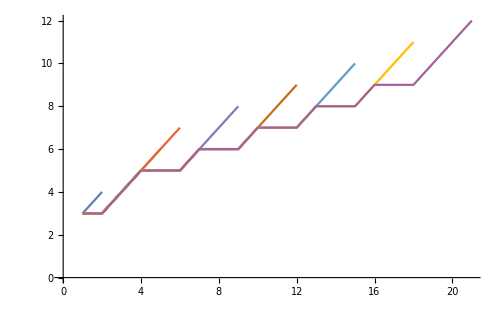
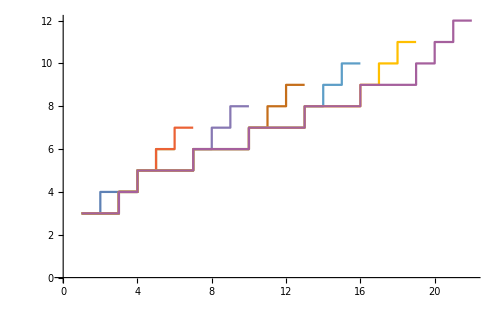
The AllPathCanyonsBinary function takes a multi-way graph and then graphically displays, with 0 and 1 as the constituents, the NestGraph generated via the multi-way tag system rule-set, and then provided the initial condition revisits the FindPath function or alternatively the FindShortestPath function on the graph such that the first & last element of the vertex list function is iterated to infinity, effectively finding all paths symbolically. 
-Graphics--Graphics-
Tag System 6
(0,0,s___) -> (0,1)
(1,0,s___)->(0,1,0)
(0,1,s___)->(1,0)
(1,1,s___)->(0,0,0)
(0,1,1)

The meaning is that as we time step from 1 to n, we are plotting the length of the current tag system throughout n time steps. On the macro point, exploring the relationship between multi-way and single-way behavior, the interaction between multi-way and single-way behavior is that visualizing generational plots that are explosive, degenerate, and periodic, the cycles depend on which path we take in the multi-way tag system. Because the function AllPathCanyons designs all tag systems at once, we can isolate single tag systems from the multi-way tag system graph and likewise the single tag systems from the plots provided, allowing us to visualize black and pink squares that represent 1 and 0 respectively, and that show the progression of a single-way tag system captured as a moment in the multi-way tag system graph vertex. By bringing the plots out of nested tables we are able to plot them overlaid together, and highlight all paths and shortest paths along the multi-way graph, because the tag system above is a generally explosive single-way behavior across paths, the graph naturally tends to increment by a length of 1 but only when the conditions (1, 0) and (1, 1) are met somewhere in the string, since we can replace at any point in the string. Probably because our two-length tag system rules are manifesting cyclically. 

The question is if any, what is the bijection between single-way and multi-way behavior? The bijection is that single-way behavior is manifested in each multi-way graph, if we follow the vertices.

## Section 3. Interesting Tag Systems.

The shifted Post tag system variant can be rendered with entries not just on the right side but also on the left side, which leads to a significant contribution from the left. The distributed spatial Post tag system looks like this,

The Post Tag System.

(..., 0, ...)->(0, 0)
(..., 1, ...)->(1, 1, 0, 1)
(1, 0, 1)

```mathematica
init={{1,0,1},{1},{0}};
graphPost:= Multicolumn[Table[With[{
g=NestGraph[ReplaceList[{
{0,left___, left___,s___}:>{s,0,0},
{1,left___, left___,s___}:>{s,1,1,0,1}
}],
{init[[i]]},
3,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality",
ImageSize->Large]},
Labeled[
HighlightGraph[
Graph[
g,
VertexLabels->Thread[VertexList[g]->(Length[#]&/@VertexList[g])]
],
Style[PathGraph[FindShortestPath[g,First[VertexList[g]],VertexList[g][[Length[VertexList[g]]]]],DirectedEdges->True],Red]
],
StringTemplate["{left___, 0, s___}->`a`
{left___, 1, s___}->`b`
`e`"]
[<|
"a"->{0,0},
"b"->{1,1,0,1},
"e":>init[[i]]
|>]]],{i,1, 3}]]
graphPost
```

-Graphics-{left___, 0, s___}->{0, 0}
{left___, 1, s___}->{1, 1, 0, 1}
{1, 0, 1} | -Graphics-{left___, 0, s___}->{0, 0}
{left___, 1, s___}->{1, 1, 0, 1}
{0}
-Graphics-{left___, 0, s___}->{0, 0}
{left___, 1, s___}->{1, 1, 0, 1}
{1} |

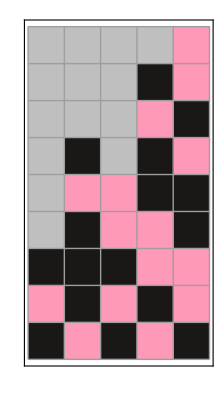
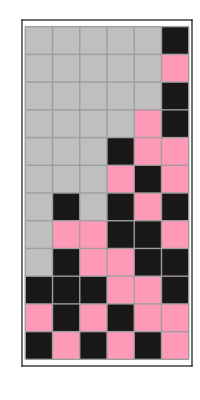
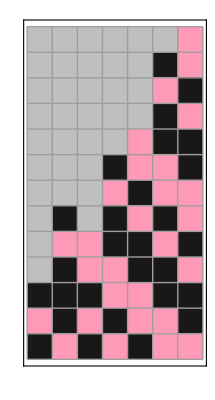
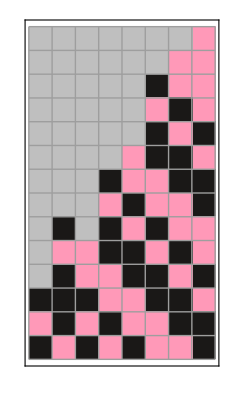
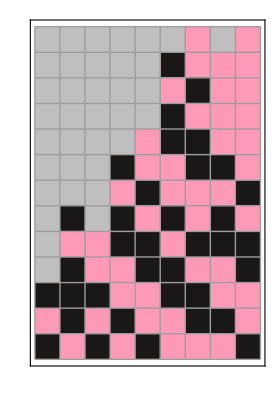
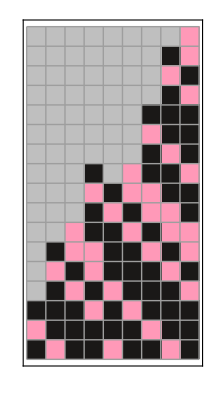
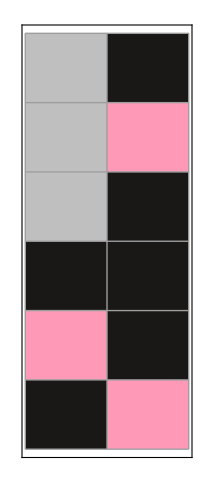
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |

```mathematica
Multicolumn[AllPathCanyons[
NestGraph[
ReplaceList[{
{0,left___,left___,s___}:>{s,0,0},
{1,left___,left___,s___}:>{s,1,1,0,1}
}],
{{1,0,1}},
8,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"
]
],Alignment->Right]
```

Typically most often the tag system rules 1 and 0 are expressed such that the 1101 pattern doubles 0 and results in the rule alternating through the initial string, for which the head should catch up with the tail eventually.

```mathematica
oneRuleAllInitialConditions[lengthInitialConditionR_,lastTimeStep_]:=
Table[ListStepPlot[Legended[FlattenAt[
 Table[
Style[Text[
With[
{
graph = NestGraph[
ReplaceList[{
{0,left___,left___,s___}:>{left,s,0,0},
{0,left___,left___,s___}:>{left,s,1,1,0,1}
}],
{Tuples[{0,1},i][[j]]},
timeStep,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"
]
},
Table[
Length /@FindShortestPath[graph,First[VertexList[graph]],VertexList[graph][[v]]],
{v,1,Length[VertexList[graph]]}
]
]]][[1]][[1]],
{timeStep,1,lastTimeStep}
]
,
{#}&/@Range[lastTimeStep]],Tuples[{0,1},i][[j]]]],
{i,lengthInitialConditionR[[1]],lengthInitialConditionR[[2]]},
{j,1,2^i}]
oneRuleAllInitialConditions[{2,3},10]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

The Distributed Spatial Post Tag System.

```mathematica
init={{1,0,1},{1},{0}};
graphPost:= Multicolumn[Table[With[{
g=NestGraph[ReplaceList[{
{left___,0,s___}:>{s,0,0},
{left___,1,s___}:>{s,1,1,0,1}
}],
{init[[i]]},
3,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality",
ImageSize->Large]},
Labeled[
HighlightGraph[
Graph[
g,
VertexLabels->Thread[VertexList[g]->(Length[#]&/@VertexList[g])]
],
Style[PathGraph[FindShortestPath[g,First[VertexList[g]],VertexList[g][[Length[VertexList[g]]]]],DirectedEdges->True],Red]
],
StringTemplate["{left___, 0, s___}->`a`
{left___, 1, s___}->`b`
`e`"]
[<|
"a"->{0,0},
"b"->{1,1,0,1},
"e":>init[[i]]
|>]]],{i,1, 3}]]
graphPost
```

-Graphics-{left___, 0, s___}->{0, 0}
{left___, 1, s___}->{1, 1, 0, 1}
{1, 0, 1} | -Graphics-{left___, 0, s___}->{0, 0}
{left___, 1, s___}->{1, 1, 0, 1}
{0}
-Graphics-{left___, 0, s___}->{0, 0}
{left___, 1, s___}->{1, 1, 0, 1}
{1} |

Shortest Path for three time steps is 101->011101->11011101->10111011101..., which, at regular intervals creates the shortest path from rule 1->1101 of Post’s tag system, whereas if there is a 0 at the beginning then rule 0->00 can clear the graph; the ___ operator allows us to open more possibilities to find the shortest path, allowing the base case of the Post tag system to be left shifted from explosive to degenerate behavior with initial condition 101. And what about the initial condition 0 which generates 00... the shortest path also happens to be the only path.

```mathematica
Multicolumn[AllPathCanyons[
NestGraph[
ReplaceList[{
{left___,0,s___}:>{s,0,0},
{left___,1,s___}:>{s,1,1,0,1}
}],
{{1,0,1}},
8,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"
]
],Alignment->Right]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |

This roughly manifests as, according to the lengths of the strings, the distributed spatial Post tag system applied to the Length property.

```mathematica
oneRuleAllInitialConditions[lengthInitialConditionR_,lastTimeStep_]:=
Table[ListStepPlot[Legended[FlattenAt[
 Table[
Style[Text[
With[
{
graph = NestGraph[
ReplaceList[{
{left___,0,s___}:>{left,s,0,0},
{left___,1,s___}:>{left,s,1,1,0,1}
}],
{Tuples[{0,1},i][[j]]},
timeStep,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"
]
},
Table[
Length /@FindShortestPath[graph,First[VertexList[graph]],VertexList[graph][[v]]],
{v,1,Length[VertexList[graph]]}
]
]]][[1]][[1]],
{timeStep,1,lastTimeStep}
]
,
{#}&/@Range[lastTimeStep]],Tuples[{0,1},i][[j]]]],
{i,lengthInitialConditionR[[1]],lengthInitialConditionR[[2]]},
{j,1,2^i}]
oneRuleAllInitialConditions[{2,3},4]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

One of the most interesting things about the Post tag system is that the initial condition of 0 begets 0s whereas on the other hand with the initial condition of 1, spatial tag system continuity is maintained. The following is the scale upon which the second rule of the shifted Post tag system, (left..., 1, s...)->(left..., s..., 1, 1, 0, 1) is stacked under the first 1 & on the last 1.

```mathematica
Multicolumn[AllPathCanyons[
NestGraph[
ReplaceList[{
{left___,0,s___}:>{s,0,0},
{left___,1,s___}:>{s,1,1,0,1}
}],
{{1}},
5,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"
]
],Alignment->Right]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |

Here, the initial condition is {1}, for which elements keep on getting removed from the tail and added to the head, which means that we can quickly generate sequences of 0s. 

Let's take the initial condition from 1 to 1, 1 ,0, 1, with the initial Post tag system that represents removing elements from the head.

```mathematica
Multicolumn[AllPathCanyons[
NestGraph[
ReplaceList[{
{0, left___, left___,s___}:>{s,0,0},
{1, left___, left___,s___}:>{s,1,1,0,1}
}],
{{1}},
5,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"
]
],Alignment->Right]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- |

```mathematica
OneDimensionAllAdjacency[
l1_,l2_,
i1R_,i2R_,
init_,
timeSteps_,
branchialGraph_:True,
matrixForm_:True
]:=With[{
graph=NestGraph[ReplaceList[
{
{left___,0,s___}:>{left,s,0,0},
{left___,1,s___}:>{left,s,1,1,0,1}
}
],
{init},
t,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"]
},
Table[
{
Labeled[
ArrayPlot[GraphDistanceMatrix[{{"[◼]", "BranchialGraph"}}[graph]]/.∞->0,ColorFunction->"TemperatureMap", PlotLegends->Automatic],
StringTemplate["{left___,0,s___}->`a`
{left___,1,s___}->`b`
`e`"]
[<|
"a"->{0,0},
"b"->{1,1,0,1},
"e":>init
|>]],
If[branchialGraph,{{"[◼]", "BranchialGraph"}}[graph],Null],
If[matrixForm,Style[MatrixForm[GraphDistanceMatrix[{{"[◼]", "BranchialGraph"}}[graph]]],FontSize->8],Null]
},
{t,1,timeSteps},
{i1, i1R[[1]],i1R[[2]]},
{i2,i2R[[1]],i2R[[2]]}
] 
]

OneDimensionAllAdjacency[
2,2,
{1,2^2},{1,2^2},
{1,1,0,1},
3,
True,
True
]
```

-Graphics-

The generation of a 5-complete graph is seen on the graph distance matrix for the Post Tag system, with regard to the distance matrices. Because, our tag systems can be designed to create 4-cycles; for instance, cycling through rules 4, 3, 2, and 1, we can still generate interesting observed tag systems. 

The graph distance matrix diagonal identity for which blue indicates a distance of 0 or infinity, for which on the other hand the graph distance matrix & branchial graph functions are colorizing the scale on 0, 1, ... and for which values of 0 are ice cold and values of n roughly correspond to the time step n that is burning up. 

the 5th time step for the rules, is Tag System 7 which generates so many fractal-like tag system shapes that this tag system initial condition 0, 1, 0 is in layers of black color where 1s are pushed toward the top of the tag system so that the 0, 0 -> 0, 0, 1 rule is anywhere, right or left of the string allowing for untouched strings of 0, 0, 1 to be maintained because in this single-way tag system, 1s will simply pile up above 0, 0, 1; that is one of the most exciting relationships between single-way and multi-way behavior that has ever been seen, because even though we may not follow to the end of the branch we definitely observe the recurrence of 0, 0, ..., 0. 

Tag System 7.
(0,  0) -> (0, 0, 1)
(1, 0) -> (0, 1, 1)
(0, 1) -> (0, 1, 1)
(1, 1) -> (0, 1, 1)
(0, 1, 0)

Leading to a checkerboard-like shape with accompanying ListLinePlot. The 7th step completes the rules for Tag System 7 which allows sequential squares to be generated, for which the first rule transmutes 10->011, as well as 01 into 011, such that the colors of the squares seem to be inverted.

```mathematica
AllPathCanyons[
NestGraph[
ReplaceList[{
{left___,0,0,s___}:>{left,s,0,0,1},
{left___,1,0,s___}:>{left,s,0,1,1},
{left___,0,1,s___}:>{left,s,0,1,1},
{left___,1,1,s___}:>{left,s,0,1,1}
}],
{{0,1,0}},
7,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"
]
]
```

Tag System 8.
(0, 0, s___) -> (1, 0)
(1, 0, s___) -> (0, 1, 1)
(0, 1, s___) -> (1, 1)
(1, 1, s___) -> (0, 0, 0)
(1, 1, 1)

-Graphics-

The values before the heat map are expressed in Matrix Form. 

(0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | 2 | 2 | 4 | 3 | 4 | 3 | 3 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | 2 | 2 | 4 | 3 | 4 | 3 | 3 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | 1 | 1 | 3 | 2 | 3 | 2 | 2 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 2 | 1 | 0 | 1 | 3 | 2 | 3 | 2 | 2 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 2 | 1 | 1 | 0 | 2 | 1 | 2 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 4 | 4 | 3 | 3 | 2 | 0 | 1 | 1 | 2 | 2 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 3 | 3 | 2 | 2 | 1 | 1 | 0 | 1 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 4 | 4 | 3 | 3 | 2 | 1 | 1 | 0 | 2 | 2 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 3 | 3 | 2 | 2 | 1 | 2 | 1 | 2 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 3 | 3 | 2 | 2 | 1 | 2 | 1 | 2 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 2 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 0 | 2 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 2 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 1 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 2 | 2 | 2 | 2 | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | 1 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 1 | 0 | 2 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 1 | 2 | 0 | 2 | 1 | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 1 | 1 | 2 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 1 | 1 | 1 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | 1 | 1
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | 1 | 1
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | 1 | 1
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 1 | 0 | 1
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 1 | 1 | 0)

Are all single-way paths in a multi-way system similar in behavior? 
(0, 0) -> (0, 1)
(1, 0) -> (0, 1, 0)
(0, 1) -> (1, 0)
(1, 1) -> (0, 0, 0)
(0, 1, 1)
makes differential single-way paths. 

Tag System 6.

-Graphics-

Tag System 2. 
(0,0,s___) -> (0, 1)
(1,0,s___) -> (0, 1, 0)
(0,1,s___ ) -> (1, 0)
(1,1,s___) -> (0, 0, 0)
(0, 1, 1)

```mathematica
The ListStepPlot function, for which AllPathCanyonsBinary already records the length, has cyclic similarity in behavior in 4 steps.
```

Branchial graph for the tag system with 4-complete and 5-complete cycles.

```mathematica
{{"[◼]", "BranchialGraph"}}[ResourceFunction["NestGraphTagged"][
ReplaceList[{
{left___,0,0,s___}:>Flatten[{left,s,0,0,0}],
{left___,1,0,s___}:>Flatten[{left,s,0,0,0}],
{left___,0,1,s___}:>Flatten[{left,s,1,1}],
{left___,1,1,s___}:>Flatten[{left,s,1,0,1}]
}],
{{1,1,1}},
5,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"
]]
```

-Graphics-

The partial state of completion shows the progression of nearly complete graphs in time steps, numerous disjoint sets which are “almost” 5-complete. 
(0,0,s___)->(1, 0, 0)
(1,0,s___)->(0, 1, 1)
(0,1,s___)->(1, 0, 1)
(1,1,s___)->(1, 1, 1)
(1, 1, 0}
-Graphics-
The idea is that there is only ever one zero supplied by the initial condition, the first tag system rule never gets invoked and for some reason we are still able to rotate around the last three rules, probably because all strings of two 1s or more can be re-written to generate three 1s while the section of the string that still has a 0 is shifted around with additional 1s at least from tag system rules (1,0,s___)->(0, 1, 1) and (0,1,s___)->(1, 0, 1). The shortest path seems to be the one that is shifted around? 
-Graphics-

Set::write: Tag Inherited in Inherited[State] is Protected.

Multi-Way Graph for All Tag System Rules

```mathematica
Multicolumn[Table[
Labeled[NestGraph[ReplaceList[{
{left___,0,0,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i1]]}],
{left___,1,0,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i2]]}],
{left___,0,1,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i3]]}],
{left___,1,1,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i4]]}]
}],
{Tuples[{0,1},l][[k]]},
t,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"],
StringTemplate["{0, 0}->`a`
{1, 0}->`b`
{0, 1}->`c`
{1, 1}->`d`
`e`"]
[<|
"a"->Tuples[{0,1},j][[i1]],
"b"->Tuples[{0,1},j][[i2]],
"c":>Tuples[{0,1},j][[i3]],
"d":>Tuples[{0,1},j][[i4]],
"e":>Tuples[{0,1},l][[k]]
|>]
],
{t,1,10},
{i1,2^j,2^j},
{i2,2^j,2^j},
{i3,2^j,2^j},
{i4,2^j,2^j},
{j,3,3},
{k,2^l,2^l},
{l,3,3}]/.{{{{{{{x_}}}}}}} -> x]
```

-Graphics-{0, 0}->{1, 1, 1}
{1, 0}->{1, 1, 1}
{0, 1}->{1, 1, 1}
{1, 1}->{1, 1, 1}
{1, 1, 1} | -Graphics-{0, 0}->{1, 1, 1}
{1, 0}->{1, 1, 1}
{0, 1}->{1, 1, 1}
{1, 1}->{1, 1, 1}
{1, 1, 1} | -Graphics-{0, 0}->{1, 1, 1}
{1, 0}->{1, 1, 1}
{0, 1}->{1, 1, 1}
{1, 1}->{1, 1, 1}
{1, 1, 1} | -Graphics-{0, 0}->{1, 1, 1}
{1, 0}->{1, 1, 1}
{0, 1}->{1, 1, 1}
{1, 1}->{1, 1, 1}
{1, 1, 1}
-Graphics-{0, 0}->{1, 1, 1}
{1, 0}->{1, 1, 1}
{0, 1}->{1, 1, 1}
{1, 1}->{1, 1, 1}
{1, 1, 1} | -Graphics-{0, 0}->{1, 1, 1}
{1, 0}->{1, 1, 1}
{0, 1}->{1, 1, 1}
{1, 1}->{1, 1, 1}
{1, 1, 1} | -Graphics-{0, 0}->{1, 1, 1}
{1, 0}->{1, 1, 1}
{0, 1}->{1, 1, 1}
{1, 1}->{1, 1, 1}
{1, 1, 1} | 
-Graphics-{0, 0}->{1, 1, 1}
{1, 0}->{1, 1, 1}
{0, 1}->{1, 1, 1}
{1, 1}->{1, 1, 1}
{1, 1, 1} | -Graphics-{0, 0}->{1, 1, 1}
{1, 0}->{1, 1, 1}
{0, 1}->{1, 1, 1}
{1, 1}->{1, 1, 1}
{1, 1, 1} | -Graphics-{0, 0}->{1, 1, 1}
{1, 0}->{1, 1, 1}
{0, 1}->{1, 1, 1}
{1, 1}->{1, 1, 1}
{1, 1, 1} |

Tag System 3.
(0,0,s___) -> (0, 0, 1)
(1,0,s___) -> (0, 0, 1)
(0,1,s___ ) -> (0, 0, 1)
(1,1,s___) -> (0, 0, 1)
(1, 0, 0)

## Compare behaviors of different paths.

## Generation Plot. Abiding by the rules (left___,0,0,s___) -> (left, s, 1,0) (left___,1,0,s___) -> (0,1,1) (left___,0,1,s___) -> (1,1) (left___,1,1,s___) ->{0,0,0) (1,1,1) we can derive explosive and straight paths. There are many behaviors to consider, because it’s a multi-way system at 10 steps. Portraying the effect of rule length 2, which transfers (left___, 0, 0, s___) to (left, s, 1, 0) and (left___, 0, 1, s___) to (left, s, 1, 1), when the paths are exploding they create (0, 1, 0) and (0, 0, 0) while when the paths are maintaining the same length they create the patterns (1, 0) and (1, 1). Focus on the new idea for tag systems, for which they can pick up the rules from anywhere in the string. Distributed, interior tag systems, also known as stag systems, are not really tag systems! In order to get something to decay, the (1, 0) for instance has to be shortened; in the Post tag system one is chopping off three at the beginning and either getting two added or four added, and that’s why it’s the marginal case. In the Post tag system, one is chopping off three at the beginning and either getting two added or four added, and the tag system is always going to explode because the length is always getting bigger. -Graphics- ListLinePlot of Lengths With the same tag system rule (Tag System Example #2 with initial condition (0,1,0)), (0, 0) -> (0, 1) (1, 0) -> (0, 1, 0) (0, 1) -> (1, 0) (1, 1) -> (0, 0, 0) It’s possible to find the shortest length path in terms of path length. For instance, the block of code Length /@ FindShortestPath[g, First[VertexList[g]], VertexList[g][[Length[VertexList[g]]]]] allows us to find the length array of the given tag system; and if we ant to find a longer array, then increase the number of time steps, inclusive of the first step. The finding for this one is that having a tag system comprised of different lengths for the initial rules results in a linearly increasing shortest path, to delineate nothing regarding paths that are perhaps longer and still produce explosive behavior in that cyclically, in four-step for our particular example, exhibits an explosion when the current string can only be rewritten with expansive rules (that is rules which rewrite the string to a higher dimension) and stalls flatly when the current string can only be rewritten with diminishing rules, that is rules which map greater lengths to equal or lesser lengths. Question: For time steps 1,2, ..., n, what does the tag system rule (0, 0) -> (0, 1) (1, 0) -> (0, 1, 0) (0, 1) -> (1, 0) (1, 1) -> (0, 0, 0) (0, 1, 0) look like in terms of our ListStepPlot function? -Graphics- State Transition Graphs & GraphDistanceMatrix Array Plot. Suppose we have the rule-set (0, 0, s___) -> (1, 0) (1, 0, s___) -> (0, 1, 1) (0, 1, s___) -> (1, 1) (1, 1, s___) -> (0, 0, 0) (1, 1, 1) -Graphics--Graphics--Graphics--Graphics--Graphics--Graphics- Based on this example, it appears that the “tag system branches” are tangentially-related, the explosive nature of which is reflected in this graph. Let’s take a closer look. -Graphics- Depending on which branch you follow, your string might decrease in size or increase in size. These tag systems have similarity across the board, for instance the fact that our stratification is repeating like a fractal. On the temperature plots we are able to see the degree of similarity between tag systems, that is 0 across the first diagonal, while infinity is also treated as 0 for the sake of visualizing the degrees of similarity from 1 to 4. If we want to look at a partially permuted version of the previous tag system we can look at (0, 0) -> (1, 1, 1) (1, 0) -> (0, 0, 1) (0, 1) -> (1, 1, 0) (1, 1) -> (0, 1, 1) (0, 0, 1) which gives the following behavior.

-Graphics-

The behavior of this tag system is manifest in the branchial graph (and numerical adjacency matrix) for this graph, 
-Graphics-

## Confluence To be quite honest, it’s questionable whether these multi-way graphs are confluent at all. The behavior of the multi-way graph for (0, 0) -> (1, 1, 1) (1, 0) -> (0, 0, 1) (0, 1) -> (1, 1, 0) (1, 1) -> (0, 1, 1) (0, 0, 1) is indicative of the multi-way evolution of tag systems for which, on the first branch for the third graph it is evident that there are two branches, because the first element is represented by (0, 0, 1) and thus can be converted either to (1, 1, 1) or to (0, 1, 1, 0), which is the rule specified by (0, 1, s___) -> (1, 1, 0). Once we have all those 1s, which can then be converted into (0, 1, 1) somewhere which adds the first 0, we are able to reconstruct all rules. In the event that either the tag system points toward coordinates with diminished dimensions, or the tag system is simply constructed such that only 1s are available, then, there could be degenerate behavior in that we might enter an extreme feedback loop. In this case we have (1, 1) -> (0, 1, 1) that prevents such a feedback loop from occurring. Likewise with the 0s except that perhaps there are other ways of forming a feedback loop that leads to degenerate tag system behavior. -Graphics-{0,0,s___}->{1, 1, 1} {1,0,s___}->{0, 0, 1} {0,1,s___}->{1, 1, 0} {1,1,s___}->{0, 1, 1} {0, 0, 1} Non-Cumulative Growth Rate for ListLinePlot & Histogram. (0, 0, s___) -> (1, 0) (1, 0, s___) -> (0, 1, 1) (0, 1, s___) -> (1, 1) (1, 1, s___) -> (0, 0, 0) (1, 1, 1) Multi-way behavior demonstrated does corroborate that varying length of the initial rules leads to explosive & periodic multi-way binary tag system re-writing. The only one of its kind? No. 111 1000 0011 001111 0111111 11111111 -Graphics- The observed behavior for this tag system could be that following the same sequence of multi-way steps allows patterns like -Graphics- patterns to keep repeating, because we are assigning (1, 1) to (0, 0, 0) and then assigning (1, 0) to (0, 1, 1) at any location in the string therefore the stag system allows us to visualize each reachable path which repeats on a small scale.

Branchial Graphs.

Branchial graph for the tag system with 4-complete and 5-complete cycles.

```mathematica
g = NestGraph[ReplaceList[{
{left___,0,0,s___}:>{left,s,0,0,0},
{left___,1,0,s___}:>{left,s,0,1,0},
{left___,0,1,s___}:>{left,s,1,0},
{left___,1,1,s___}:>{left,s,1,1,1}
}],
{{1,0,1}},
6,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality",
ImageSize->Full
,VertexLabels->Thread[VertexList[g]->(Length[#]&/@VertexList[g])]
]

Labeled[g,
StringTemplate["{0,0,s___}->`a`
{1,0,s___}->`b`
{0,1,s___}->`c`
{1,1,s___}->`d`
`e`"]
[<|
"a"->{0,0,0},
"b"->{0,1,0},
"c":>{1,0},
"d":>{1,1,1},
"e":>{1,0,1}
|>]
]

HighlightGraph[g,Style[PathGraph[FindShortestPath[g,First[VertexList[g]],VertexList[g][[Length[VertexList[g]]]]],DirectedEdges->True],Red]]
```

-Graphics-

-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{1, 1, 1}
{1, 0, 1}

-Graphics-

Tag System 6. 
(0,0,s___) -> (0, 0, 0)
(1,0,s___) -> (0, 1, 0)
(0,1,s___) -> (1, 0)
(1,1,s___) -> (1, 1, 1)
(1, 0, 1)
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
Even though we’re trying to generate a sequence of 1, 1, 1, ..., 1, it seems that the multi-way tag system initial condition value of 1, 0, 1 allows the tag system to, due to the multi-way nature of the plots, alternatively push the existing 1s further up the graph with the application of the 0, 0 rule that is the first rule (once a second 0 is generated by (1,0,s___) -> (0, 1, 0) and (0,1,s___) -> (1, 0) or combine the two into a staggered 0, 1, 0 or alternatively, 1, 0 plot in which we generate something that looks like a staircase... the multi-way characteristic is coming from the distributed stag system with left___.

## Concluding remarks

To summarize in conclusion, providing future plans & ideas for extension of the work, it would be brilliant to engage in further explorations of interesting tag system behavior. Whereas if we are implementing the tag system with different lengths for the rules, such as (0,0)->(0,1), (1,0)->(0,1,0), (0,1)->(1,0), and (1,1)->(0,0,0), it appears that the greatest factor in generating explosive behavior is variability in the initial conditions’ length. Applying this same tag system rule to the initial NestGraph which is the basis for our ListStepPlot in that we are taking the length of each path in the multi-way NestGraph, the shortest path from the initial state to the end state is the one in which the initial condition (0, 1, 0) is essentially inverted by the tag system. 
-Graphics-
The evidence suggests that the confluence of systems is consistent across permutations of tag systems. The multi-computational behavior mentioned is most evident via the alteration of initial rules, which can across our four and eight initial rules tend toward the degenerate forms, which typically do not arise due to the nature of string rewriting. 

The single-way behavior makes it clear that as long as the paths are connected in the branchial, adjacency matrix then they are related in the sense that they are able to continue without going into a self-destructive cycle of degeneracy. The meaning behind this is that this tag system, and the single-way behavior in the sense of tag system length, is likely to be regularly incremental. 

Question: What are some of the ways to reduce computational complexity such that we are able to compute these tag system rules across vast time steps? 

The initial condition as a proxy for its corresponding rules determines the shortest path, because the graph searches for the corresponding rules which may or may not include the absolute shortest path (absolute across the multi-way system).

## Keywords

Post Tag System

String Rewriting

Multi-Way & One-Way

## Acknowledgment

Props go to James for being such a kind mentor; and Stephen Wolfram defining the direction of this project toward methodically working upward. And to Post for providing the principal tag system.

## References

Mentor James Boyd, who teaches us keyboard shortcuts instead of Command + V. His passion (for entailment cones and) for multi-way computation in tag systems, and his insistence on having us meet with Nik, really kept things going.

Nik Murzin, whose generation of TwoWayMultiReplace has been nothing less than instrumental because he is the one who provides the scope and options for functions like TwoWayMultiReplace, with Identity, Uniquify, Canonicalize, and KeyMap Associations in .m nonetheless. Nik wrote things like Utilities, TwoWayRule, SubexpressionPositions, Rewriting, Quantifiers, MultiReplace, MultiCoReplace, MultiBiReplace, Metamathematics, Legacy, and Inference. He actually understands how the Mathematica kernel works!

Nik also does things like equational logic, axiomatic theory, and equation proof. When he is building the kernel, he builds things like Graph, LinkedHypergraph, Multicomputation, MulticomputationLoader, MulticomputationMain, MultiStringReplace, Utilities, and WFR. In fact, it is Nik who has created Tuples, HoldTuples, MatchSubstitutions. It’s so important for focusing on tag systems. It is Nik who has allowed the tag system rules to be applied anywhere in the current string.

Credit goes to Utkarsh for explaining how sequentality works so we didn’t think the past history had any bearing on the result of applying the tag system at any given time.

American Journal of Mathematics 1943-04: Vol 65 Iss 2 : Free Download, Borrow, and Streaming : Internet Archive
https://archive.org/details/sim_american-journal-of-mathematics_1943-04_65_2/page/202/mode/2up

After 100 Years, Can We Finally Crack Post’s Problem of Tag? A Story of Computational Irreducibility, and More—Stephen Wolfram Writings
https://writings.stephenwolfram.com/2021/03/after-100-years-can-we-finally-crack-posts-problem-of-tag-a-story-of-computational-irreducibility-and-more/#connecting-to-number-theory